```mathematica
Clear[Ross,dRoss,HRoss,dHRoss,Lor, dLor]
(* Rossler *)
(* {a,b,c} = {0.2,0.2,5.7} *)
Ross[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x+a y,b+z (x-c)}
dRoss[{a_,b_,c_}][{x_,y_,z_}]:={{0,-1,-1},{1,a,0},{z,0,x-c}}
(* Hyperchaotic Rossler *)
(* {a,b,c,d}={0.25,3,0.5,0.05} *)
HRoss[{a_,b_,c_,d_}][{x_,y_,z_,w_}]:={-y-z,x+a y+w,b+x z,-c z+d w}
dHRoss[{a_,b_,c_,d_}][{x_,y_,z_,w_}]:={{0,-1,-1,0},{1,a,0,1},{z,0,x,0},{0,0,-c,d}}
(*Lorenz*)
(* {sigma, rho, beta}={10,28,8/3} *)
Lor[{sigma_,rho_,beta_}][{x_,y_,z_}]:={sigma (y-x),x (rho-z)-y,x y-beta z};
dLor[{sigma_,rho_,beta_}][{x_,y_,z_}]:={{-sigma,sigma,0},{rho-z,-1,-x},{y,x,-beta}};
```

A cartoon for equilibria.

```mathematica
ClearAll[EqCartoon];
EqCartoon[A_]:=Module[
{vals,vecs,tol=10^-8,glyph},
{vals,vecs}=Chop[Eigensystem[N[A]]];
glyph[lam_,v_]:=Which[
Im[lam]==0,With[{e=Normalize[Re[v]],s=Sign[Re[lam]]},If[s==0,{Gray,Dashed,Line[{-e,e}]},{Blue,Table[Arrow[If[s>0,{.15 k e,k e},{k e,.15 k e}]],{k,{-1,1}}]}]],Im[lam]>0,With[{p=Normalize[Re[v]],q=Normalize[Im[v]],s=Sign[Re[lam]]},{Orange,Arrow[Table[.5 Exp[.06 s (t-2 Pi)] (Cos[t] p-Sin[t] q),{t,0,4 Pi,Pi/40}]]}],True,Nothing];
Graphics3D[{Thick,Arrowheads[.04],MapThread[glyph,{vals,vecs}],Black,PointSize[.025],Point[{0,0,0}]},Boxed->False,PlotRange->1.2,ImageSize->250]]
EqCartoon[A_,p_,s_]:=Graphics3D[
GeometricTransformation[First[EqCartoon[A]],AffineTransform[{s IdentityMatrix[3],p}]],Boxed->False,PlotRange->All,ImageSize->250]
```

Finding Equilibria

```mathematica
{a,b,c}={0.2,0.2,5.7};
Quiet[Sub = Solve[Ross[{a,b,c}][{x,y,z}]=={0,0,0},{x,y,z}];]
{eq1,eq2}={x,y,z}/.Sub;
{A1,A2}=dRoss[{a,b,c}][{x,y,z}]/.Sub;
TableForm[{λs1,vs1}=Eigensystem[A1]];
TableForm[{λs2,vs2}=Eigensystem[A2]];
y1={0.007,-0.03,0.1};
y2={5.6,-28.4,28.4};
TMax=12;
y1Sol=NDSolveValue[{ y'[t]==Ross[{a,b,c}][y[t]], y[0]==y1},y, {t, 0 ,TMax}];
z1Sol=NDSolveValue[{ y'[t]==A1.y[t], y[0]==y1-eq1},y, {t, 0 ,TMax}];
y2Sol=NDSolveValue[{ y'[t]==Ross[{a,b,c}][y[t]], y[0]==y2},y, {t, 0 ,10TMax}];
z2Sol=NDSolveValue[{ y'[t]==A2.y[t], y[0]==y2-eq2},y, {t, 0 ,TMax}];
TabView[{
"eq1"->Show[
ParametricPlot3D[{y1Sol[t],z1Sol[t]+eq1},{t,0, TMax},PlotRange->All,BoxRatios->{1, 1, 1},PlotStyle->{Red, Green}],
EqCartoon[A1,eq1,0.1]
],
"eq2"->Show[
ParametricPlot3D[{y2Sol[t],z2Sol[t]+eq2},{t,0, TMax},PlotRange->All,BoxRatios->{1,1,1},PlotStyle->{Red, Green}],
EqCartoon[A2,eq2,0.3]],
"gap"->LogLogPlot[{Norm[y1Sol[t]-(z1Sol[t]+eq1)],Norm[y2Sol[t]-(z2Sol[t]+eq2)]},{t,10^-15, TMax},PlotRange->All],
"Big Pic"->Show[
ParametricPlot3D[y2Sol[t],{t,0, 10TMax},PlotRange->All,BoxRatios->{1,1,1},PlotStyle->Directive[Thin,Red]],
EqCartoon[A2,eq2,2],
EqCartoon[A1,eq1,2]]
}]
```

1234

## Rössler Equilibrium

The plan is lower and upper side by side.  Transitions cc+r ↔3r.  Sign transitions on rs and re[ccs].

We want to compute, plot  and understand manifolds etc. How they change when we mess with the parameters (a,b,c) .

The equilibria are

 | y_1 | y_2 | y_3
lower | 1/2 (c-√(-4 a b+c^2)) | 1/2 (-c/a+(√(-4 a b+c^2))/a) | (c-√(-4 a b+c^2))/(2 a)
upper | 1/2 (c+√(-4 a b+c^2)) | 1/2 (-c/a-(√(-4 a b+c^2))/a) | (c+√(-4 a b+c^2))/(2 a)
There are two real equilibria if d=-4 a b+c^2>0.  The equilibria are complex (and thus not relevant for our real ODE) if d<0.  We are going to build a 3D picture of the behavior.   When the equilibria are real the ones with the

```mathematica
StdParams={{0.2,0.2,5.7},{0.2,0.2, 2.6}};
Show[
Plot3D[ √(4 a b), {a, 0, 1},{b,0,1},
PlotStyle->Opacity[0.5],
AxesLabel->{"a","b","c"}],
ListPointPlot3D[StdParams],
PlotRange->All
]
```

-Graphics3D-

The eigenvalues  are the roots of 

"lower" | 1/2 (((c-√(-4 a b+c^2)) (a-λ))/a+(c+√(-4 a b+c^2)+2 λ) (-1+a λ-λ^2))==0
"upper" | 1/2 (((c+√(-4 a b+c^2)) (a-λ))/a+(c-√(-4 a b+c^2)+2 λ) (-1+a λ-λ^2))==0
This would look a lot cleaner if we gave √(-4 a b+c^2) a name.  It makes sense to tidy up as we go along. I am going to call
	 δ=√(-4 a b+c^2)
We should look at what we have and decide if we can make it cleaner!

```mathematica
TidierSub={c-√(-4 a b+c^2)->2a p,-c+√(-4 a b+c^2)->-2a p, c+√(-4 a b+c^2)->2a q};
EqSub=Simplify[Solve[Ross[{a,b,c}][{x,y,z}]=={0,0,0},{x,y,z}]]/.TidierSub;
Map[MatrixForm,{AL,AU}=dRoss[{a,b,c}][{x,y,z}]/.EqSub];
{pL[λ_],pU[λ_]}=Map[CharacteristicPolynomial[#,λ]&,{AL,AU}];
Collect[{pL[λ],pU[λ]},λ]
{dL,dU}=Map[Discriminant[#,λ]&,{pL[λ],pU[λ]}];
```

{-c+2 a p+(-1+a c-p-a^2 p) λ+(a-c+a p) λ^2-λ^3,-c+2 a q+(-1+a c-q-a^2 q) λ+(a-c+a q) λ^2-λ^3}

```mathematica
ContourPlot3D[dU,{a,0,1},{q,0,1},{c,0, 7},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
MatrixForm[AL]
```

(0 | -1 | -1
1 | a | 0
p | 0 | -c+a p)

```mathematica
?Discriminant
```

```mathematica
Map[MatrixForm,Simplify[dRoss[{a,b,c}][{x,y,z}]/.EqSub]]
```

{{x→(a p)/2,y→(-c+√(-4 a b+c^2))/(2 a),z→p/2},{x→(a q)/2,y→-(c+√(-4 a b+c^2))/(2 a),z→q/2}}

{(0 | -1 | -1
1 | a | 0
p/2 | 0 | -c+(a p)/2),(0 | -1 | -1
1 | a | 0
q/2 | 0 | -c+(a q)/2)}

```mathematica
Clear[a,b,c,δ]
{A1,A2}=dRoss[{a,b,c}][{x,y,z}]/.Sub/.{√(-4 a b+c^2)->δ};
(* {A1,A2}={A1,A2}/.{c-δ-> 2 p a,c+δ-> 2 q a }; *)
TableForm[
Map[MatrixForm,Simplify[{A1,A2}]],
TableHeadings->{{"lower","upper"}}]

TableForm[{
Collect[CharacteristicPolynomial[A1,λ]==0,λ],
Collect[CharacteristicPolynomial[A2,λ]==0,λ]},
TableHeadings->{{"lower","upper"}}]
```

ReplaceAll::reps: {Sub} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {A1,A2} and {{0,-1,-1},{1,a,0},{z,0,-c+x}}/.Sub are not the same shape.

lower | A1
upper | A2

lower | CharacteristicPolynomial[A1,λ]==0
upper | CharacteristicPolynomial[A2,λ]==0

The roots of these characteristic polynomials are the eigenvalues of the linear approximation matrices at the equilibria.  Is this a good picture of the lower polynomial

2.77128-14.9253 λ+0.185641 λ^2-λ^3

{{λ→-0.0000178189-3.86333 ⅈ},{λ→-0.0000178189+3.86333 ⅈ},{λ→0.185676}}

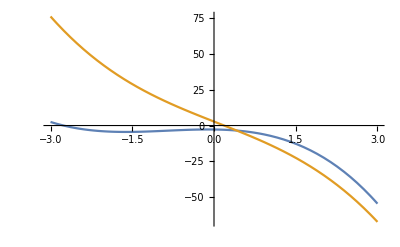

```mathematica
Clear[a,b,c,δ,fL, fU,λ]
{a,b,c}={0.2,0.2,2.8};
δ=√(-4 a b+c^2);
fL[λ_]=-δ+(-1-c/(2 a)+(a c)/2+δ/(2 a)+(a δ)/2) λ+(a-c/2-δ/2) λ^2-λ^3;
fU[λ_]=δ+(-1+a c-(c+δ)/(2 a)-1/2 a (c+δ)) λ+(a-c+(c+δ)/2) λ^2-λ^3
Solve[fU[λ]==0,λ]
Plot[{fL[λ],fU[λ]},{λ,-3,3}]
```

## Lorenz Equilibrium